## Setup

Note: we use m,c as variables instead of u,v here

### PDE Solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->100,"BC"->"Reflective"}];
runTwoComponentSim[{f_,g_},params_,{mInit_,cInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{D[m[x,t],t]==Dm D[m[x,t],{x,2}]+(f/.{m->m[x,t],c->c[x,t]}),D[c[x,t],t]==Dc D[c[x,t],{x,2}]+(g/.{m->m[x,t],c->c[x,t]}),If[OptionValue["BC"]==="Periodic",{m[0,t]==m[L,t],c[0,t]==c[L,t],(D[m[x,t],x]/.x->0)==(D[m[x,t],x]/.x->L),(D[c[x,t],x]/.x->0)==(D[c[x,t],x]/.x->L)},{(D[m[x,t],x]/.x->0)==0,(D[c[x,t],x]/.x->0)==0,(D[m[x,t],x]/.x->L)==0,(D[c[x,t],x]/.x->L)==0}],m[x,0]==mInit[x],c[x,0]==cInit[x]}/.params,{m,c},{x,0,L/.params},{t,0,tMax},Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},(*Choose higher scale factor to enforce boundary conditions in case the initial condition does not fulfil them*)"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}];
```

### Finite Differences Setup

Mass-conserving two-component reaction diffusion system using m,c as variables.

```mathematica
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]/dx^2
]
```

#### Stationary state equations

```mathematica
setupFiniteDifferenceEqs[f_,gridRes_]:=With[{
mVec=Thread[m@Range[gridRes]],
cVec=Thread[c@Range[gridRes]],
fm=D[f,m],fc=D[f,c]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"mVec"->mVec,
"Vars"->Join[mVec,{η}],
"Eqs"->{
Dm discreteLaplace[mVec,L/gridRes]+(f/.c->η-Dm/Dc m/.m->mVec),
 η+(1-Dm/Dc)Total@mVec/gridRes-n
},
"DynJacobian"->D[Join[
Dm discreteLaplace[mVec,L/N[gridRes]]+(f/.{c->cVec,m->mVec}),
Dc discreteLaplace[cVec,L/N[gridRes]]-(f/.{c->cVec,m->mVec})
],
{Join[mVec,cVec]}
]/.c[i_]:>η-Dm/Dc m[i]
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_,t_]:=Join[
Transpose[{
fdSetup["mVec"],
m[x,t]/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
{{η,c[0,t]+Dm/Dc m[0,t]/.params/.initSol}}
]
```

#### Jacobian for “glued” system, assuming antisymmetry of modes

```mathematica
laplaceMatrixAS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-3,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
```

```mathematica
Options@constructGluedJacobianAS={"Reverse"->False};
constructGluedJacobianAS[params_,statSol_,dfdu_,OptionsPattern[]]:=
With[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
statSol[[1;;-2]],
statSol[[-1]]-(Dm/Dc/.params) statSol[[1;;-2]]
}],
dfduP=dfdu/.params,
gridRes=(Length@statSol-1)
},
KroneckerProduct[laplaceMatrixAS[gridRes],DiagonalMatrix[{Dm,Dc}/(L/gridRes)^2/.params]]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{m,c}->solVec[[i]]]),
{i,gridRes}
]
]
]
```

### Model setup

```mathematica
params={Dm->SetPrecision[0.1,100],Dc->SetPrecision[1,100],L->10};
f=m^2c-m;
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[f,200];
```

## n̄-sweep

```mathematica
Off[FindRoot::lstol]
```

```mathematica
dn=(1-Dm/Dc)/Sqrt[Dm/(2Dc)]/.params;
mmax=1/Sqrt[Dm/(2Dc)]/.params;
nmin=3Sqrt[Dm/(2 Dc)]/.params;
```

```mathematica
nbarMin=nmin+dn/2-1;
nbarMax=nmin+dn/2+1;
```

### Init

```mathematica
initRun=runTwoComponentSim[
{f,-f},
params,
{nbarMin(1+Cos[Pi#/L])&,0&},
1000
];
```

```mathematica
initSol=Block[{m},FindRoot[
fdSetup["Eqs"]/.Join[{n->nbarMin},params],
getInitGuess[fdSetup,params,initRun,1000]
]
];//AbsoluteTiming
```

{0.061976,Null}

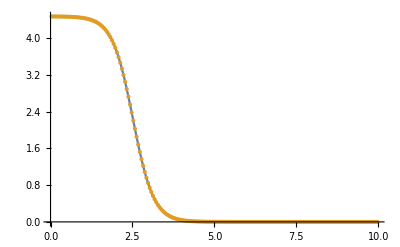

```mathematica
ListPlot[Transpose/@{
{x,m[x,1000]/.initRun}/.x->(L/.params) fdSetup["UnitGrid"],
{(L/.params) fdSetup["UnitGrid"],fdSetup["mVec"]/.initSol}
},
PlotRange->All,
Joined->{True,False}
]
```

#### Plots of profiles at min and max nbar of the sweep

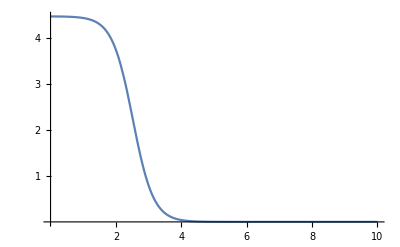

```mathematica
Plot[m[x,1000]/.initRun/.params,{x,0,L/.params},
Ticks->{{2,4,6,8,10},{1,2,3,4}}
]
```

```mathematica
nbarMaxRun=runTwoComponentSim[
{f,-f},
params,
{nbarMax(1+Cos[Pi#/L])&,0&},
1000
];
```

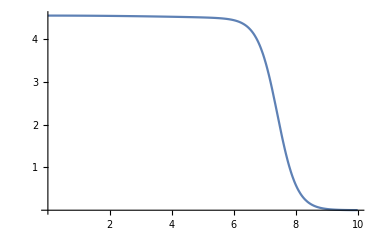

```mathematica
Plot[m[x,1000]/.nbarMaxRun/.params,{x,0,L/.params},
Ticks->{{2,4,6,8,10},{1,2,3,4}}
]
```

#### Run

```mathematica
nbarSweep=Block[{m,c,sol,prevSol=initSol,σNp,σNm,Lp},
Monitor[Table[
sol=FindRoot[
fdSetup["Eqs"]/.Join[{n->SetPrecision[nbarIter,100]},params],
prevSol/.Rule->List,
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100
];

σNp=Eigenvalues[Normal@constructGluedJacobianAS[
params,
sol[[All,2]],
D[{f,-f},{{m,c}}],
"Reverse"->False
],-1,Method->{"Arnoldi","Tolerance"->10^-20}][[-1]];
σNm=Eigenvalues[Normal@constructGluedJacobianAS[
params,
sol[[All,2]],
D[{f,-f},{{m,c}}],
"Reverse"->True
],-1,Method->{"Arnoldi","Tolerance"->10^-20}][[-1]];

Lp=L(nbarIter-3 Sqrt[Dm/(2Dc)])Sqrt[Dm/(2 Dc)]/(1-Dm/Dc)/.params;

prevSol=sol;
{
nbarIter,
sol,
σNp,
6 (√Dm)/(1-Dm/Dc)1/(L-Lp)Exp[-2Lp/√Dm]/.params,
σNm,
6 (√Dm)/(1-Dm/Dc)1/Lp Exp[-2(L-Lp)/√Dm]/.params
},
{nbarIter,nbarMin,nbarMax, 0.1}
],
Row[{"Progress: ",Round[(nbarIter-nbarMin)/0.1]," of ",Round[(nbarMax-nbarMin)/0.1]}]
]];//AbsoluteTiming
```

{68.9905,Null}

#### Plot

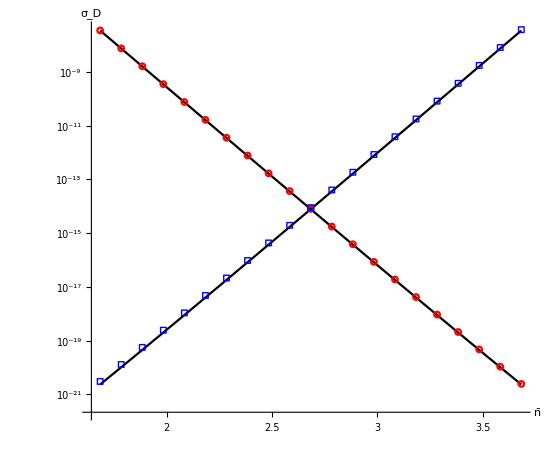

```mathematica
ListLogPlot[{
nbarSweep[[All,{1,-4}]],
nbarSweep[[All,{1,-2}]],
nbarSweep[[All,{1,-3}]],
Transpose@{nbarSweep[[All,1]],nbarSweep[[All,-1]]}
},
Joined->{False,False,True,True},
AspectRatio->5/6,
AxesStyle->Directive[Black],
PlotMarkers->{
{Graphics@{Red,Circle[]},0.03},{Graphics@{FaceForm[None],EdgeForm[{Blue,AbsoluteThickness[1]}],Rectangle[]},0.03},
None,None
},
Ticks->{
{2,2.5,3,3.5},
{{10^-20,"10^-20"},{10^-15,"10^-15"},{10^-10,"10^-10"}}
},
AxesLabel->{OverBar[n],Subscript[σ, "D"]},
BaseStyle->{Black,14},
TicksStyle->Directive[Black]
]
```